```mathematica
Clear["Global`*"]
notation ={wa->Subscript[ω, a],wo->Subscript[ω, 0],wp->Subscript[ω, p],delta->Δ, cb ->Subscript[c, b] ,ca ->Subscript[c, a],
uab->Subscript[μ, ab],uba->Subscript[μ, ba],  eps ->ℰ, cbnp1 -> Subscript[c,b,n+1], cn0 -> Subscript[c, n0]};
```

g2 plot from theory paper (plot repeated in matlab)

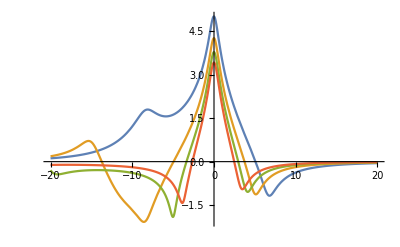

```mathematica
k = 1;
gamma=k;
eps = 0.01;

dap = da - I*k/2;
dop = do -I*gamma/2;
C2g = (eps^2* ((dap + dop)*dop + g^2))/(Sqrt[2](dap*dop-g^2)*((dap+dop)*dap-g^2));
C1g = (eps*dop)/(g^2-dap*dop);
g2 = (2*Abs[C2g]^2)/Abs[C1g]^4;
lg2 = Log10[g2];
strongc = lg2 /.g->10;
Plot[{strongc /.da->15,strongc /.da->20,strongc /.da->25,strongc /.da->30}, {do,-20,20},PlotRange->All]
```

Section A
Energy eigenvalues for strong coupling

```mathematica
H = {{n*wa,g*Sqrt[n]},{g*Sqrt[n],wo+(n-1)*wa}};
MatrixForm[H] /. notation
En=Eigenvalues[H];
Eminus = En[[1]];
Eplus = En[[2]];
```

(n ω_a | g √n
g √n | ω_0+(-1+n) ω_a)

Section B
Coefficients for g2

```mathematica
Psi = {c0g[t], c1g[t],c0e[t],c2g[t],c1e[t]}; MatrixForm[Psi]
```

(c0g[t]
c1g[t]
c0e[t]
c2g[t]
c1e[t])

```mathematica
lhs = D[Psi, t];

eqlist1= Thread[rhs == lhs]; MatrixForm[eqlist1] /. notation
```